```mathematica
Monitor[Table[allGraphs5[k,"generators"]=FlatGenerators[allGraphs5[k,"colofour"]],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
FullBaseCoeff5[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs5[#,"colofour"]&,allGraphs5AtomKeys]}],CompareSymbols]}]
```

```mathematica
Sort[Table[var,{var,Map[allGraphs5[#,"colofour"]&,allGraphs5AtomKeys]}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}

```mathematica
EmptyBaseCoeff5[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs5[#,"colofourrealnull"]&,allGraphs5NullAtomKeys]}],CompareSymbols]}]
```

```mathematica
FullBaseCoeff5[allGraphs5[0,"colofour"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
theGens5=Sort[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[ListofVars[allGraphs5[#,"generators"]]]==1&],CompareSymbols[First[allGraphs5[#1,"generators"]],First[allGraphs5[#2,"generators"]]]&];
```

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"v"->prefix]]
```

```mathematica
repGen5=First[Solve[Table[ChangeSymbol[First[allGraphs5[k,"generators"]],"g"]==allGraphs5[k,"colofour"],{k,theGens5}],Table[allGraphs5[m,"colofour"],{m,allGraphs5AtomKeys}]]];
```

```mathematica
Monitor[Table[allGraphs5[k,"genfour"]=Simplify[allGraphs5[k,"colofour"]/.repGen5],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
DocValue5[key_]:=With[
{rep=Join[
Table[ChangeSymbol[k,"g"]->Style[ChangeSymbol[k,"g"],Red,Bold],{k,FlatGenerators[allGraphs5[key,"generators"]]}],
Table[k->Style[k,Red],{k,FlatGenerators[allGraphs5[key,"generators"]]}]]},
Table[allGraphs5[key,code]/.rep,{code,{"generators","genfour","colofour"}}]
]
```

```mathematica
GenIndices5[key_]:=Block[{gens=Map[ChangeSymbol[#,"g"]&,FlatGenerators[allGraphs5[key,"generators"]]],gens2=Map[ChangeSymbol[#,"v"]&,FlatGenerators[allGraphs5[key,"generators"]]],genForm=allGraphs5[key,"genfour"],
genColor=allGraphs5[key,"colofour"]},
With[{a=Table[Coefficient[genForm,var],{var,gens}],b=Table[Coefficient[genColor,var],{var,gens2}]},
{
a,
b,
a==b
}
]
]
```

```mathematica
MobGen[k_]:=With[{
m=MobiusGraph5[K5Key,allGraphs5],
gen=Map[ChangeSymbol[#,"n"]&,allGraphs5[k,"generators"]],
full=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[k,"colofour"]]]
},
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->SymbolName[v],{v,full}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

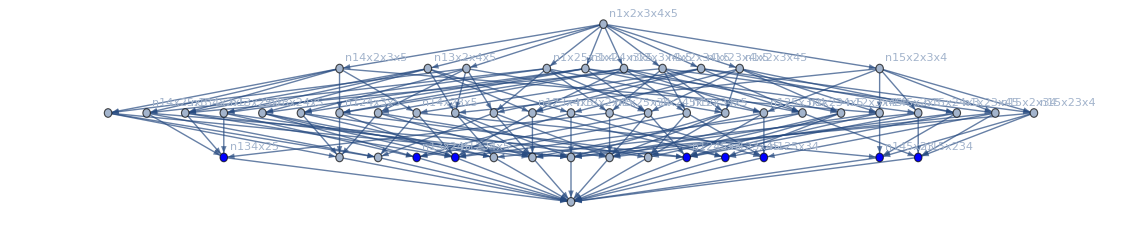

```mathematica
MobGen[3]
```

```mathematica
ChangeSymbolEmpty[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"g"->prefix]]
```

```mathematica
MobGen2[k_]:=With[{
m=MobiusGraph5[K5Key,allGraphs5],
gen=Sort[Map[ChangeSymbolEmpty[#,"n"]&,ListofVars[allGraphs5[k,"genfour"]]],CompareSymbols],
full=Sort[Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[k,"colofour"]]],CompareSymbols]
},
Labeled[
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->SymbolName[v],{v,full}],GraphLayout->"LayeredDigraphEmbedding"],
ToString[gen]==ToString[full]
]
]
```

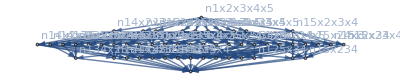
-Graphics-True

```mathematica
MobGen2[1]
```

```mathematica
XPower[sym_]:=x^(1+StringCount[SymbolName[sym],"x"])
```

```mathematica
genRep5=Table[allGraphs5[k,"genfour"]->ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,theGens5}]
```

{g1x2x3x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,g1x2x3x45→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x2x34x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x2x35x4→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x23x4x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x24x3x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x25x3x4→18 x-39 x^2+29 x^3-9 x^4+x^5,g12x3x4x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g13x2x4x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g14x2x3x5→18 x-39 x^2+29 x^3-9 x^4+x^5,g15x2x3x4→18 x-39 x^2+29 x^3-9 x^4+x^5,g1x23x45→14 x-31 x^2+24 x^3-8 x^4+x^5,g1x24x35→14 x-31 x^2+24 x^3-8 x^4+x^5,g1x25x34→14 x-31 x^2+24 x^3-8 x^4+x^5,g12x3x45→14 x-31 x^2+24 x^3-8 x^4+x^5,g12x34x5→14 x-31 x^2+24 x^3-8 x^4+x^5,g12x35x4→14 x-31 x^2+24 x^3-8 x^4+x^5,g13x2x45→14 x-31 x^2+24 x^3-8 x^4+x^5,g13x24x5→14 x-31 x^2+24 x^3-8 x^4+x^5,g13x25x4→14 x-31 x^2+24 x^3-8 x^4+x^5,g14x2x35→14 x-31 x^2+24 x^3-8 x^4+x^5,g14x23x5→14 x-31 x^2+24 x^3-8 x^4+x^5,g14x25x3→14 x-31 x^2+24 x^3-8 x^4+x^5,g15x2x34→14 x-31 x^2+24 x^3-8 x^4+x^5,g15x23x4→14 x-31 x^2+24 x^3-8 x^4+x^5,g15x24x3→14 x-31 x^2+24 x^3-8 x^4+x^5,g1x2x345→8 x-20 x^2+18 x^3-7 x^4+x^5,g1x234x5→8 x-20 x^2+18 x^3-7 x^4+x^5,g1x235x4→8 x-20 x^2+18 x^3-7 x^4+x^5,g1x245x3→8 x-20 x^2+18 x^3-7 x^4+x^5,g123x4x5→8 x-20 x^2+18 x^3-7 x^4+x^5,g124x3x5→8 x-20 x^2+18 x^3-7 x^4+x^5,g125x3x4→8 x-20 x^2+18 x^3-7 x^4+x^5,g134x2x5→8 x-20 x^2+18 x^3-7 x^4+x^5,g135x2x4→8 x-20 x^2+18 x^3-7 x^4+x^5,g145x2x3→8 x-20 x^2+18 x^3-7 x^4+x^5,g12x345→7 x-17 x^2+15 x^3-6 x^4+x^5,g123x45→7 x-17 x^2+15 x^3-6 x^4+x^5,g124x35→7 x-17 x^2+15 x^3-6 x^4+x^5,g125x34→7 x-17 x^2+15 x^3-6 x^4+x^5,g13x245→7 x-17 x^2+15 x^3-6 x^4+x^5,g134x25→7 x-17 x^2+15 x^3-6 x^4+x^5,g135x24→7 x-17 x^2+15 x^3-6 x^4+x^5,g14x235→7 x-17 x^2+15 x^3-6 x^4+x^5,g145x23→7 x-17 x^2+15 x^3-6 x^4+x^5,g15x234→7 x-17 x^2+15 x^3-6 x^4+x^5,g1x2345→x-4 x^2+6 x^3-4 x^4+x^5,g1234x5→x-4 x^2+6 x^3-4 x^4+x^5,g1235x4→x-4 x^2+6 x^3-4 x^4+x^5,g1245x3→x-4 x^2+6 x^3-4 x^4+x^5,g1345x2→x-4 x^2+6 x^3-4 x^4+x^5,g12345→x^5}

```mathematica
Table[CoefficientList[ChromaticPolynomial[allGraphs5[k,"graph"],x],x],{k,theGens5}]//MatrixForm
```

(0 | 24 | -50 | 35 | -10 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 18 | -39 | 29 | -9 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 14 | -31 | 24 | -8 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 8 | -20 | 18 | -7 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 7 | -17 | 15 | -6 | 1
0 | 1 | -4 | 6 | -4 | 1
0 | 1 | -4 | 6 | -4 | 1
0 | 1 | -4 | 6 | -4 | 1
0 | 1 | -4 | 6 | -4 | 1
0 | 1 | -4 | 6 | -4 | 1
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
fullRep5=Table[allGraphs5[k,"colofour"]->ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x3x45→-6 x+11 x^2-6 x^3+x^4,v1x2x35x4→-6 x+11 x^2-6 x^3+x^4,v1x2x34x5→-6 x+11 x^2-6 x^3+x^4,v1x2x345→2 x-3 x^2+x^3,v1x25x3x4→-6 x+11 x^2-6 x^3+x^4,v1x25x34→2 x-3 x^2+x^3,v1x24x3x5→-6 x+11 x^2-6 x^3+x^4,v1x24x35→2 x-3 x^2+x^3,v1x245x3→2 x-3 x^2+x^3,v1x23x4x5→-6 x+11 x^2-6 x^3+x^4,v1x23x45→2 x-3 x^2+x^3,v1x235x4→2 x-3 x^2+x^3,v1x234x5→2 x-3 x^2+x^3,v1x2345→-x+x^2,v15x2x3x4→-6 x+11 x^2-6 x^3+x^4,v15x2x34→2 x-3 x^2+x^3,v15x24x3→2 x-3 x^2+x^3,v15x23x4→2 x-3 x^2+x^3,v15x234→-x+x^2,v14x2x3x5→-6 x+11 x^2-6 x^3+x^4,v14x2x35→2 x-3 x^2+x^3,v14x25x3→2 x-3 x^2+x^3,v14x23x5→2 x-3 x^2+x^3,v14x235→-x+x^2,v145x2x3→2 x-3 x^2+x^3,v145x23→-x+x^2,v13x2x4x5→-6 x+11 x^2-6 x^3+x^4,v13x2x45→2 x-3 x^2+x^3,v13x25x4→2 x-3 x^2+x^3,v13x24x5→2 x-3 x^2+x^3,v13x245→-x+x^2,v135x2x4→2 x-3 x^2+x^3,v135x24→-x+x^2,v134x2x5→2 x-3 x^2+x^3,v134x25→-x+x^2,v1345x2→-x+x^2,v12x3x4x5→-6 x+11 x^2-6 x^3+x^4,v12x3x45→2 x-3 x^2+x^3,v12x35x4→2 x-3 x^2+x^3,v12x34x5→2 x-3 x^2+x^3,v12x345→-x+x^2,v125x3x4→2 x-3 x^2+x^3,v125x34→-x+x^2,v124x3x5→2 x-3 x^2+x^3,v124x35→-x+x^2,v1245x3→-x+x^2,v123x4x5→2 x-3 x^2+x^3,v123x45→-x+x^2,v1235x4→-x+x^2,v1234x5→-x+x^2,v12345→x}

```mathematica
MobGen3[k_]:=With[{
m=MobiusGraph5[K5Key,allGraphs5],
gen=allGraphs5[k,"genfour"],
full=allGraphs5[k,"colofour"]
},
Simplify[{ChromaticPolynomial[allGraphs5[k,"graph"],x], gen,full,(gen/.genRep5),(full/.fullRep5)}]
]
```

```mathematica
MobGen3[1]
```

{(-1+x) x^4,g1234x5+g1235x4-g123x4x5+g124x35-g124x3x5+g125x34-g125x3x4-g12x34x5-g12x35x4+2 g12x3x4x5+g134x25-g134x2x5+g135x24-g135x2x4-g13x24x5-g13x25x4+2 g13x2x4x5+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5-g1x235x4+2 g1x23x4x5-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4+2 g1x2x34x5+2 g1x2x35x4-6 g1x2x3x4x5,v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,(-1+x) x^4,(-1+x) x^4}

```mathematica
GenIndices5[271]
```

{{1,1,1,1,1},{1,1,1,1,1},True}

```mathematica
Table[ShowGraph[allGraphs5,k]->{Length[ListofVars[allGraphs5[k,"colofour"]]],Length[ListofVars[allGraphs5[k,"genfour"]]],Length[FlatGenerators[allGraphs5[k,"colofour"]]]},{k,Take[Keys[allGraphs5],20]}]
```

{-Graphics-0→{52,1,1},-Graphics-19683→{37,37,8},-Graphics-26244→{27,10,4},-Graphics-28431→{20,3,2},-Graphics-29160→{15,1,1},-Graphics-29403→{10,10,4},-Graphics-29484→{7,3,2},-Graphics-29511→{5,1,1},-Graphics-29520→{3,3,2},-Graphics-29523→{2,1,1},-Graphics-29524→{1,1,1},-Graphics-29525→{1,2,1},-Graphics-29527→{1,2,1},-Graphics-29521→{2,1,1},-Graphics-29529→{2,4,1},-Graphics-29533→{1,2,1},-Graphics-29537→{1,5,1},-Graphics-29514→{3,3,2},-Graphics-29515→{2,1,1},-Graphics-29517→{2,4,1}}

```mathematica
Table[ShowGraph[allGraphs5,k]->GenIndices5[k],{k,Take[Keys[allGraphs5],20]}]
```

{-Graphics-0→{{1},{1},True},-Graphics-19683→{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},True},-Graphics-26244→{{1,1,1,1},{1,1,1,1},True},-Graphics-28431→{{1,1},{1,1},True},-Graphics-29160→{{1},{1},True},-Graphics-29403→{{1,1,1,1},{1,1,1,1},True},-Graphics-29484→{{1,1},{1,1},True},-Graphics-29511→{{1},{1},True},-Graphics-29520→{{1,1},{1,1},True},-Graphics-29523→{{1},{1},True},-Graphics-29524→{{1},{1},True},-Graphics-29525→{{1},{1},True},-Graphics-29527→{{1},{1},True},-Graphics-29521→{{1},{1},True},-Graphics-29529→{{1},{1},True},-Graphics-29533→{{1},{1},True},-Graphics-29537→{{1},{1},True},-Graphics-29514→{{1,1},{1,1},True},-Graphics-29515→{{1},{1},True},-Graphics-29517→{{1},{1},True}}

```mathematica
{-Graphics-0->{{1},{1},True},-Graphics-253->{{1,1,1,1},{1,1,1,1},True},-Graphics-325->{{1,1},{1,1},True},-Graphics-351->{{1},{1},True},-Graphics-360->{{1,1},{1,1},True},-Graphics-363->{{1},{1},True},-Graphics-365->{{1},{1},True},-Graphics-365->{{1},{1},True},-Graphics-367->{{1},{1},True},-Graphics-361->{{1},{1},True},-Graphics-369->{{1},{1},True},-Graphics-373->{{1},{1},True},-Graphics-377->{{1},{1},True},-Graphics-355->{{1,1},{1,1},True},-Graphics-355->{{1},{1},True},-Graphics-357->{{1},{1},True},-Graphics-352->{{1,1},{1,1},True},-Graphics-353->{{1},{1},True},-Graphics-382->{{1},{1},True},-Graphics-391->{{1},{1},True}}
```

{-Graphics-0→{{1},{1},True},-Graphics-253→{{1,1,1,1},{1,1,1,1},True},-Graphics-325→{{1,1},{1,1},True},-Graphics-351→{{1},{1},True},-Graphics-360→{{1,1},{1,1},True},-Graphics-363→{{1},{1},True},-Graphics-365→{{1},{1},True},-Graphics-365→{{1},{1},True},-Graphics-367→{{1},{1},True},-Graphics-361→{{1},{1},True},-Graphics-369→{{1},{1},True},-Graphics-373→{{1},{1},True},-Graphics-377→{{1},{1},True},-Graphics-355→{{1,1},{1,1},True},-Graphics-355→{{1},{1},True},-Graphics-357→{{1},{1},True},-Graphics-352→{{1,1},{1,1},True},-Graphics-353→{{1},{1},True},-Graphics-382→{{1},{1},True},-Graphics-391→{{1},{1},True}}

```mathematica
Table[ShowGraph[allGraphs5,k]->DocValue5[k],{k,Take[Keys[allGraphs5],10]}]
```

{-Graphics-0→{{v12345},g12345,v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v12345},-Graphics-19683→{{v1x2345,v15x234,v14x235,v145x23,v13x245,v135x24,v134x25,v1345x2},-g134x2x5-g135x2x4-g13x24x5-g13x25x4-g13x2x45+2 g13x2x4x5-g145x2x3-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5+g1345x2+g134x25+g135x24+g13x245+g145x23+g14x235+g15x234+g1x2345,v134x2x5+v135x2x4+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v1345x2+v134x25+v135x24+v13x245+v145x23+v14x235+v15x234+v1x2345},-Graphics-26244→{{v1x2345,v15x234,v14x235,v145x23},-g14x23x5-g15x23x4-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5+g145x23+g14x235+g15x234+g1x2345,v145x2x3+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v145x23+v14x235+v15x234+v1x2345},-Graphics-28431→{{v1x2345,v15x234},-g1x234x5+g15x234+g1x2345,v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v15x234+v1x2345},-Graphics-29160→{{v1x2345},g1x2345,v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v1x2345},-Graphics-29403→{{v1x2x345,v1x25x34,v1x24x35,v1x245x3},-g1x24x3x5-g1x25x3x4-g1x2x34x5-g1x2x35x4-g1x2x3x45+2 g1x2x3x4x5+g1x245x3+g1x24x35+g1x25x34+g1x2x345,v1x24x3x5+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v1x245x3+v1x24x35+v1x25x34+v1x2x345},-Graphics-29484→{{v1x2x345,v1x25x34},-g1x2x34x5+g1x25x34+g1x2x345,v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v1x25x34+v1x2x345},-Graphics-29511→{{v1x2x345},g1x2x345,v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5+v1x2x345},-Graphics-29520→{{v1x2x3x45,v1x2x35x4},-g1x2x3x4x5+g1x2x35x4+g1x2x3x45,v1x2x3x4x5+v1x2x35x4+v1x2x3x45},-Graphics-29523→{{v1x2x3x45},g1x2x3x45,v1x2x3x4x5+v1x2x3x45}}

```mathematica
{-Graphics-0->{{v1235},g1235,v123x5+v125x3+v12x35+v12x3x5+v135x2+v13x25+v13x2x5+v15x23+v15x2x3+v1x235+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v1235},-Graphics-253->{{v1x235,v15x23,v13x25,v135x2},-g13x2x5-g15x2x3-g1x23x5-g1x25x3-g1x2x35+2 g1x2x3x5+g135x2+g13x25+g15x23+g1x235,v13x2x5+v15x2x3+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v135x2+v13x25+v15x23+v1x235},-Graphics-325->{{v1x235,v15x23},-g1x23x5+g15x23+g1x235,v15x2x3+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v15x23+v1x235},-Graphics-351->{{v1x235},g1x235,v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v1x235},-Graphics-360->{{v1x2x35,v1x25x3},-g1x2x3x5+g1x25x3+g1x2x35,v1x2x3x5+v1x25x3+v1x2x35},-Graphics-363->{{v1x2x35},g1x2x35,v1x2x3x5+v1x2x35},-Graphics-365->{{v1x2x3x5},g1x2x3x5,v1x2x3x5},-Graphics-365->{{v1x2x35},-g1x2x3x5+g1x2x35,v1x2x35},-Graphics-367->{{v1x25x3},-g1x2x3x5+g1x25x3,v1x25x3},-Graphics-361->{{v1x25x3},g1x25x3,v1x2x3x5+v1x25x3}}
```

{-Graphics-0→{{v1235},g1235,v123x5+v125x3+v12x35+v12x3x5+v135x2+v13x25+v13x2x5+v15x23+v15x2x3+v1x235+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v1235},-Graphics-253→{{v1x235,v15x23,v13x25,v135x2},-g13x2x5-g15x2x3-g1x23x5-g1x25x3-g1x2x35+2 g1x2x3x5+g135x2+g13x25+g15x23+g1x235,v13x2x5+v15x2x3+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v135x2+v13x25+v15x23+v1x235},-Graphics-325→{{v1x235,v15x23},-g1x23x5+g15x23+g1x235,v15x2x3+v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v15x23+v1x235},-Graphics-351→{{v1x235},g1x235,v1x23x5+v1x25x3+v1x2x35+v1x2x3x5+v1x235},-Graphics-360→{{v1x2x35,v1x25x3},-g1x2x3x5+g1x25x3+g1x2x35,v1x2x3x5+v1x25x3+v1x2x35},-Graphics-363→{{v1x2x35},g1x2x35,v1x2x3x5+v1x2x35},-Graphics-365→{{v1x2x3x5},g1x2x3x5,v1x2x3x5},-Graphics-365→{{v1x2x35},-g1x2x3x5+g1x2x35,v1x2x35},-Graphics-367→{{v1x25x3},-g1x2x3x5+g1x25x3,v1x25x3},-Graphics-361→{{v1x25x3},g1x25x3,v1x2x3x5+v1x25x3}}

```mathematica
GenBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Table[ChangeSymbol[First[allGraphs5[k,"generators"]],"g"],{k,theGens5}]}],CompareSymbols]}]
```

```mathematica
Table[With[{c=EmptyBaseCoeff5[allGraphs5[k,"colofourrealnull"]]},{Min[c],Max[c]}],{k,theGens5}]//Tally
```

{{{-6,24},1},{{-6,18},10},{{-4,14},15},{{-4,8},10},{{-3,7},10},{{-1,1},5},{{0,1},1}}

```mathematica
{{{-6,2},1},{{-5,2},6},{{-3,1},3},{{-1,1},5},{{0,1},1}}
```

{{{-6,2},1},{{-5,2},6},{{-3,1},3},{{-1,1},5},{{0,1},1}}

```mathematica
{{{-120,25},1},{{-95,25},15},{{-78,18},55},{{-55,18},20},{{-55,15},15},{{-55,15},50},{{-15,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},5},{{0,1},1}}
```

{{{-120,25},1},{{-95,25},15},{{-78,18},55},{{-55,18},20},{{-55,15},15},{{-55,15},50},{{-15,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},5},{{0,1},1}}

```mathematica
{{{-120,25},1},{{-95,25},15},{{-78,18},55},{{-55,18},20},{{-55,15},15},{{-55,15},50},{{-15,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},5},{{0,1},1}}
```

{{{-120,25},1},{{-95,25},15},{{-78,18},55},{{-55,18},20},{{-55,15},15},{{-55,15},50},{{-15,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},5},{{0,1},1}}

```mathematica
EmptyBaseCoeff5[allGraphs5[1,"colofourrealnull"]]
```

{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
theGens5Comp=Table[FindComplement[k,allGraphs5],{k,theGens5}]
```

{0,1,9,3,243,81,27,19683,6561,2187,729,244,84,36,19684,19692,19686,6562,6642,6588,2190,2430,2214,738,972,810,13,333,273,109,26487,21951,20439,8757,7293,2917,19696,26488,21954,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29524}

```mathematica
SummarizeGenerators[k_]:=Block[{gen=BaseGenerators[allGraphs5[k,"colofour"]],keys},
keys=Keys[gen];
Table[{kk,Length[gen[kk]]},{kk,Sort[keys]}]]
```

```mathematica
SummarizeGenerators[1]
```

{{2,8}}

```mathematica
{{2,5}}
```

{{2,5}}

```mathematica
Table[SummarizeGenerators[k],{k,theGens5Comp}]
```

{{{1,1}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{5,1}}}

```mathematica
{{{1,1}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{5,1}}}
```

{{{1,1}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,5}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{5,1}}}

```mathematica
Multicolumn[Table[Framed[Labeled[{
ShowGraph[allGraphs5,k],
ShowGraph[allGraphs5,FindComplement[k,allGraphs5]]
},SymbolToLabel2[allGraphs5[k,"generators"]//First,5],Top]],{k,theGens5}],8,Appearance->"Horizontal"]
```

{-Graphics-29524,-Graphics-0}OverHat[1] | {-Graphics-29523,-Graphics-1}45 | {-Graphics-29515,-Graphics-9}34 | {-Graphics-29521,-Graphics-3}35 | {-Graphics-29281,-Graphics-243}23 | {-Graphics-29443,-Graphics-81}24 | {-Graphics-29497,-Graphics-27}25 | {-Graphics-9841,-Graphics-19683}12
{-Graphics-22963,-Graphics-6561}13 | {-Graphics-27337,-Graphics-2187}14 | {-Graphics-28795,-Graphics-729}15 | {-Graphics-29280,-Graphics-244}23♁45 | {-Graphics-29440,-Graphics-84}24♁35 | {-Graphics-29488,-Graphics-36}25♁34 | {-Graphics-9840,-Graphics-19684}12♁45 | {-Graphics-9832,-Graphics-19692}12♁34
{-Graphics-9838,-Graphics-19686}12♁35 | {-Graphics-22962,-Graphics-6562}13♁45 | {-Graphics-22882,-Graphics-6642}13♁24 | {-Graphics-22936,-Graphics-6588}13♁25 | {-Graphics-27334,-Graphics-2190}14♁35 | {-Graphics-27094,-Graphics-2430}14♁23 | {-Graphics-27310,-Graphics-2214}14♁25 | {-Graphics-28786,-Graphics-738}15♁34
{-Graphics-28552,-Graphics-972}15♁23 | {-Graphics-28714,-Graphics-810}15♁24 | {-Graphics-29511,-Graphics-13}345 | {-Graphics-29191,-Graphics-333}234 | {-Graphics-29251,-Graphics-273}235 | {-Graphics-29415,-Graphics-109}245 | {-Graphics-3037,-Graphics-26487}123 | {-Graphics-7573,-Graphics-21951}124
{-Graphics-9085,-Graphics-20439}125 | {-Graphics-20767,-Graphics-8757}134 | {-Graphics-22231,-Graphics-7293}135 | {-Graphics-26607,-Graphics-2917}145 | {-Graphics-9828,-Graphics-19696}12♁345 | {-Graphics-3036,-Graphics-26488}123♁45 | {-Graphics-7570,-Graphics-21954}124♁35 | {-Graphics-9076,-Graphics-20448}125♁34
{-Graphics-22854,-Graphics-6670}13♁245 | {-Graphics-20740,-Graphics-8784}134♁25 | {-Graphics-22150,-Graphics-7374}135♁24 | {-Graphics-27064,-Graphics-2460}14♁235 | {-Graphics-26364,-Graphics-3160}145♁23 | {-Graphics-28462,-Graphics-1062}15♁234 | {-Graphics-29160,-Graphics-364}2345 | {-Graphics-760,-Graphics-28764}1234
{-Graphics-2278,-Graphics-27246}1235 | {-Graphics-6816,-Graphics-22708}1245 | {-Graphics-20034,-Graphics-9490}1345 | {-Graphics-0,-Graphics-29524}OverHat[0] |  |  |  |

```mathematica
{{{-Graphics-365,-Graphics-0}OverHat[1], {-Graphics-363,-Graphics-1}"35", {-Graphics-355,-Graphics-9}"23", {-Graphics-361,-Graphics-3}"25", {-Graphics-121,-Graphics-253}"12", {-Graphics-283,-Graphics-81}"13", {-Graphics-337,-Graphics-27}"15", {-Graphics-120,-Graphics-255}"12""♁""35"}, {{-Graphics-280,-Graphics-85}"13""♁""25", {-Graphics-328,-Graphics-36}"15""♁""23", {-Graphics-351,-Graphics-13}"235", {-Graphics-31,-Graphics-333}"123", {-Graphics-91,-Graphics-273}"125", {-Graphics-255,-Graphics-109}"135", {-Graphics-0,-Graphics-365}OverHat[0], ""}}
```

{-Graphics-365,-Graphics-0}OverHat[1] | {-Graphics-363,-Graphics-1}35 | {-Graphics-355,-Graphics-9}23 | {-Graphics-361,-Graphics-3}25 | {-Graphics-121,-Graphics-253}12 | {-Graphics-283,-Graphics-81}13 | {-Graphics-337,-Graphics-27}15 | {-Graphics-120,-Graphics-255}12♁35
{-Graphics-280,-Graphics-85}13♁25 | {-Graphics-328,-Graphics-36}15♁23 | {-Graphics-351,-Graphics-13}235 | {-Graphics-31,-Graphics-333}123 | {-Graphics-91,-Graphics-273}125 | {-Graphics-255,-Graphics-109}135 | {-Graphics-0,-Graphics-365}OverHat[0] |

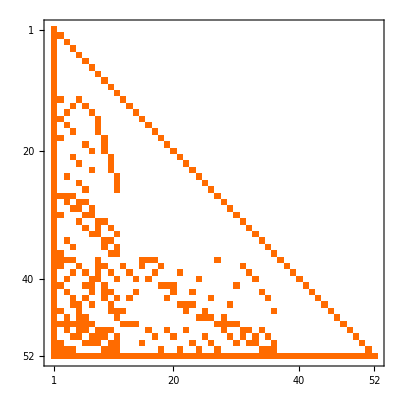

```mathematica
mat=Table[
FullBaseCoeff5[allGraphs5[k,"colofour"]],
{k,theGens5}
];MatrixPlot[mat]
```

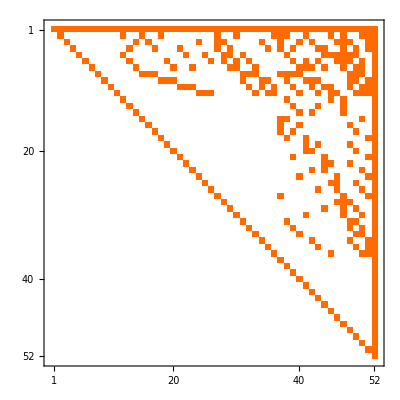

```mathematica
mat2=Table[
FullBaseCoeff5[allGraphs5[k,"colofour"]],
{k,Sort[allGraphs5NullAtomKeys,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]}
];MatrixPlot[mat2]
```

```mathematica
mat==Transpose[mat2]
```

True

## Mobius and zeta

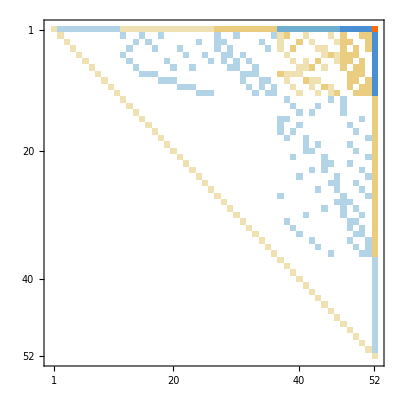

```mathematica
mob5=MobiusMatrix[allGraphs5];MatrixPlot[mob5]
```

```mathematica
zeta5=Inverse[mob5];MatrixPlot[zeta5]
```

-Graphics-

```mathematica
zeta5Transp=Transpose[zeta5];MatrixPlot[zeta5Transp]
```

-Graphics-

```mathematica
T
```

T

```mathematica
Monitor[Table[allGraphs5[k,"fullbasecoeff"]=FullBaseCoeff5[allGraphs5[k,"colofour"]],{k,Sort[Keys[allGraphs5]]}],k]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,0,0,0,1,1,0,1,1,1,0,1,0,1,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,1,0,0,0,1,0,1,0,0,1,1,1},1889,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
Monitor[Table[allGraphs5[k,"emptybasecoeff"]=EmptyBaseCoeff5[allGraphs5[k,"colofourrealnull"]],{k,Sort[Keys[allGraphs5]]}],k]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1889,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
Map[ShowGraph[allGraphs5,#]&,Monitor[
Table[
Select[Keys[allGraphs5],allGraphs5[#,"fullbasecoeff"]==zeta5Transp[[k]]&]//First,
{k,1,52}
],
k]]
```

{-Graphics-29524,-Graphics-29523,-Graphics-29515,-Graphics-29521,-Graphics-29281,-Graphics-29443,-Graphics-29497,-Graphics-9841,-Graphics-22963,-Graphics-27337,-Graphics-28795,-Graphics-29280,-Graphics-29440,-Graphics-29488,-Graphics-9840,-Graphics-9832,-Graphics-9838,-Graphics-22962,-Graphics-22882,-Graphics-22936,-Graphics-27334,-Graphics-27094,-Graphics-27310,-Graphics-28786,-Graphics-28552,-Graphics-28714,-Graphics-29511,-Graphics-29191,-Graphics-29251,-Graphics-29415,-Graphics-3037,-Graphics-7573,-Graphics-9085,-Graphics-20767,-Graphics-22231,-Graphics-26607,-Graphics-9828,-Graphics-3036,-Graphics-7570,-Graphics-9076,-Graphics-22854,-Graphics-20740,-Graphics-22150,-Graphics-27064,-Graphics-26364,-Graphics-28462,-Graphics-29160,-Graphics-760,-Graphics-2278,-Graphics-6816,-Graphics-20034,-Graphics-0}

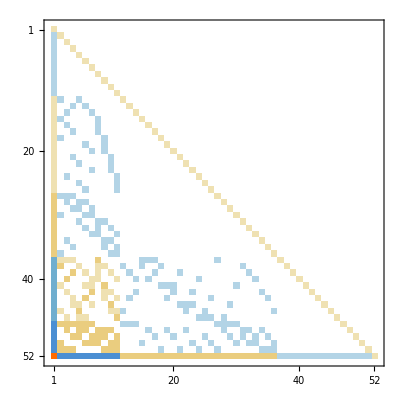

```mathematica
mob5Transp=Transpose[mob5];MatrixPlot[mob5Transp]
```

```mathematica
ZeroOne[vect_]:=Table[If[vect[[kk]]≠0,1,0],{kk,Length[vect]}]
```

```mathematica
FakeNull=Table[
Select[Keys[allGraphs5],ZeroOne[allGraphs5[#,"emptybasecoeff"]]==ZeroOne[mob5Transp[[k]]]&]//First,
{k,1,52}
]
```

{0,1,9,3,243,81,27,19683,6561,2187,729,244,84,36,19684,19692,19686,6562,6642,6588,2190,2430,2214,738,972,810,13,333,273,109,26487,21951,20439,8757,7293,2917,19696,26488,21954,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29524}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"genfour"]]]&,FakeNull]
```

{1,37,37,37,37,37,37,37,37,37,37,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,17,17,17,17,17,17,17,17,17,17,13,13,13,13,13,13,13,13,13,13,5,5,5,5,5,1}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofour"]]]&,FakeNull]
```

{52,37,37,37,37,37,37,37,37,37,37,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,17,17,17,17,17,17,17,17,17,17,13,13,13,13,13,13,13,13,13,13,5,5,5,5,5,1}

```mathematica
Map[Length[allGraphs5[#,"vertexsets"]]&,FakeNull]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
Map[EdgeCount[allGraphs5[#,"graph"]]&,FakeNull]
```

{0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,10}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofournull"]]]&,FakeNull]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofourrealnull"]]]&,FakeNull]
```

{1,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,10,10,10,10,10,10,10,10,10,10,15,15,15,15,15,52}

```mathematica
MatrixRank[Map[FullBaseCoeff5[allGraphs5[#,"colofour"]]&,FakeNull]]
```

52

```mathematica
Map[ShowGraph[allGraphs5,#]&,FakeNull]
```

{-Graphics-0,-Graphics-1,-Graphics-9,-Graphics-3,-Graphics-243,-Graphics-81,-Graphics-27,-Graphics-19683,-Graphics-6561,-Graphics-2187,-Graphics-729,-Graphics-244,-Graphics-84,-Graphics-36,-Graphics-19684,-Graphics-19692,-Graphics-19686,-Graphics-6562,-Graphics-6642,-Graphics-6588,-Graphics-2190,-Graphics-2430,-Graphics-2214,-Graphics-738,-Graphics-972,-Graphics-810,-Graphics-13,-Graphics-333,-Graphics-273,-Graphics-109,-Graphics-26487,-Graphics-21951,-Graphics-20439,-Graphics-8757,-Graphics-7293,-Graphics-2917,-Graphics-19696,-Graphics-26488,-Graphics-21954,-Graphics-20448,-Graphics-6670,-Graphics-8784,-Graphics-7374,-Graphics-2460,-Graphics-3160,-Graphics-1062,-Graphics-364,-Graphics-28764,-Graphics-27246,-Graphics-22708,-Graphics-9490,-Graphics-29524}

```mathematica
allGraphs5[9490,"emptybasecoeff"]
```

{1,-1,-1,-1,0,0,0,0,-1,-1,-1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,2,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0}

```mathematica
-mob5Transp[[51]]
```

{6,-2,-2,-2,0,0,0,0,-2,-2,-2,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0}

```mathematica
allGraphs5[2214,"compwhy"]
```

The relation holds x2214== x21897(Greater) + 42390 (Greater)

```mathematica
mob5Transp[[52]]
```

{24,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1}

```mathematica
Table[
Select[Keys[allGraphs5],allGraphs5[#,"emptybasecoeff"]==Reverse[mob5Transp[[k]]]&],
{k,1,52}
]
```

{{59048},{39014},{52232},{56770},{58288},{29888},{30586},{32684},{31984},{36898},{38308},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{31954},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
{{728},{573},{637},{697},{377},{500},{548},{},{},{},{},{},{},{},{}}
```

```mathematica
ShowGraph[allGraphs4,400]
```

-Graphics-400

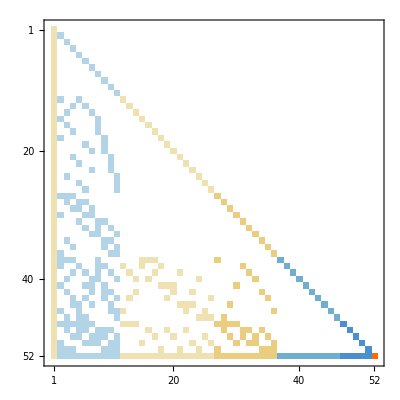

```mathematica
compSomthing=Table[allGraphs5[k,"emptybasecoeff"],{k,Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofournull"]]]==1&],CompareSymbols[allGraphs5[#1,"colofournull"],allGraphs5[#2,"colofournull"]]&]}];MatrixPlot[compSomthing]
```

```mathematica
daig=Diagonal[(mob5Transp.compSomthing)]
```

{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6}

```mathematica
Diagonal[(compSomthing.mob5Transp)]
```

{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6}

```mathematica
compSomthing.daig
```

{1,2,2,2,2,2,2,4,4,4,8,8,8,8,62}